```mathematica
SetDirectory["/home/xidad/CLionProjects/LJ-Gas/cmake-build-release"]
```

/home/xidad/CLionProjects/LJ-Gas/cmake-build-release

```mathematica
allData= Table[Import[ToString@k,"Table"],{k,0,118800,200}];
(*coords =Partition[#,2]&/@ data[[2;;]];*)
```

```mathematica
|
```

```mathematica
Clear@data
```

```mathematica
ls[k_] := Graphics[
{
Table[Point[{particle[[1]],particle[[2]]}],{particle,allData[[k]]}]
},PlotRange->{{0,500},{0,500}},Frame->True,ImageSize->Large]
```

```mathematica
anim = ListAnimate@Table[ls[k],{k,1,Length@allData}]
```

```mathematica
tempData=allData[[1]];
velocities[data_]:= Table[√(particle[[3]]^2+particle[[4]]^2),{particle,data}];
```

```mathematica
hist[k_]:=Histogram[(velocities[allData[[k]]]),{0.1},"PDF",PlotTheme->"Scientific",PlotRange->{{0,4},Automatic}]
```

```mathematica
animHist= ListAnimate@Table[hist[k],{k,1,Length@allData}]
```

Thread::tdlen: Objects of unequal length in {4.775,5.225}+{4.775,5.225}+«47»+{0.025,0.2,0.4,0.675,0.575,0.85,1.,0.775,0.8,0.725,0.925,0.7,0.35,0.575,0.275,0.3,0.275,0.15,0.125,0.1,0.025,0.075,0.05,0.025,0.025}+«950» cannot be combined.

Thread::tdlen: Objects of unequal length in {9.55,10.45}+{0.025,0.025,0.1,0.075,0.175,0.125,0.175,0.125,0.325,3.55,4.35,0.325,0.275,0.275,0.075}+«47»+{0.075,0.3,0.325,0.45,0.6,0.725,0.6,0.825,0.825,0.95,0.85,0.675,0.4,0.6,0.35,0.3,0.325,0.325,0.175,0.075,0.125,0.,0.075,0.025,0.025}+«949» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

BarChart::ldata: ({9.55,10.45}+{0.025,0.025,0.1,0.075,0.175,0.125,0.175,0.125,0.325,3.55,4.35,0.325,0.275,0.275,0.075}+«48»+«949»)/1000 is not a valid dataset or list of datasets.

BarChart[({9.55,10.45}+997+{0.1,0.15,0.35,0.375,0.45,0.425,0.575,0.425,0.6,0.325,0.575,0.45,0.8,0.375,1257,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.025})/1000,PlotTheme→Scientific,PlotRange→{{0,4},Automatic}]
 |  |  |  |

```mathematica
Length@allData
```

595

```mathematica
aver=(Sum[Normal@BinCounts[(velocities[allData[[k]]]),{bc}],{k,150,Length@allData}]/(Length@allData-150));
averData=Table[{0.1(i),aver[[i]]},{i,1,Length@aver}];
norm=NIntegrate[Interpolation[averData][x],{x,0,4}];
aver=(Sum[Normal@BinCounts[(velocities[allData[[k]]]),{bc}],{k,150,Length@allData}]/(Length@allData-150))/norm;
averData=Table[{0.1(i),aver[[i]]},{i,1,Length@aver}];
σ=
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

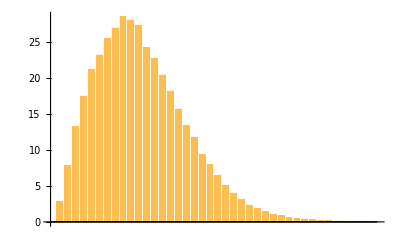

```mathematica
BarChart@aver
```

```mathematica
bc=Table[i,{i,0,4,0.1}];
```

```mathematica
PDF[MaxwellDistribution[σ],x]
```

Piecewise[{{(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3, x>0}, {0, True}}]

```mathematica
pdf[x_]:=2x Exp[-x^2]
```

```mathematica
fit[k_]:=FindFit[velocities[allData[[k]]],pdf[x],σ,x]
```

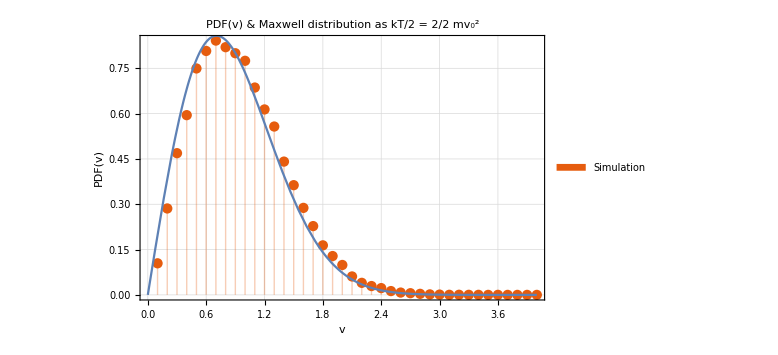

```mathematica
Show[{ListPlot[{averData},PlotTheme->"Scientific",PlotRange->{{0,4},Automatic},Filling->Axis,ImageSize->Large,BaseStyle->FontSize->20,GridLines->Automatic,FrameLabel->{"v","PDF(v)"},PlotLegends->SwatchLegend[{"Simulation"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],PlotLabel->"PDF(v) & Maxwell distribution as kT/2 = 2/2 mv_0^2"],Plot[pdf[x],{x,0,4}]}]
```

```mathematica
|
```

```mathematica
Clear[σ]
```

```mathematica
Median[velocities[allData[[800]]]]
```

1.09527

```mathematica
pdf[x]/.σ->Median[velocities[allData[[800]]]]
```

0.607269 ⅇ^(-0.416803 x^2) x^2

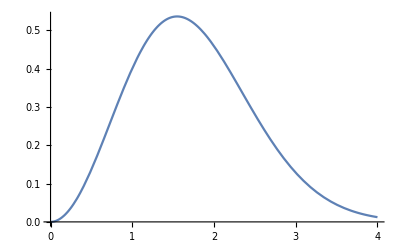

```mathematica
Plot[pdf[x]/.σ->Median[velocities[allData[[800]]]],{x,0,4}]
```

```mathematica
pdf[x]/.fit[1]
```

1.16977×10^-6 ⅇ^(-0.0000645272 x^2) x^2

```mathematica
pdf[x]/.fit[800]
```

3.06184 ⅇ^(-1.22555 x^2) x^2

```mathematica
Export["plot.png",plt]
```

plot.png

```mathematica
tst={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
Table[Line/@coords[[1;;k;;Max[1,Floor[Length@coords/100]],i]],{i,1,k}]/.k->4
```

Table::iterb: Iterator {i,1,k} does not have appropriate bounds.

Part::partw: Part 3 of {{-1,0},{1,0}} does not exist.

Part::pkspec1: The expression Line[1;;4;;10] cannot be used as a part specification.

Part::partw: Part 4 of {{-1,0},{1,0}} does not exist.

Part::pkspec1: The expression Line[1;;4;;10] cannot be used as a part specification.

{{Line[{-1,0}]},2,Line[{{{-1,0},{1,0}},{{-0.99495,0.005},{0.99495,-0.005}},{{-0.989849,0.00999975},{0.989849,-0.00999975}},{{-0.984698,0.014999},{0.984698,-0.014999}},{{-0.979495,0.0199974},{0.979495,-0.0199974}},{{-0.97424,0.0249948},{0.97424,-0.0249948}},{{-0.968932,0.0299908},{0.968932,-0.0299908}},{{-0.963571,0.0349852},{0.963571,-0.0349852}},{{-0.958156,0.0399777},{0.958156,-0.0399777}},{{-0.952687,0.0449678},{0.952687,-0.0449678}},982,{{-0.154279,0.363117},{0.154279,-0.363117}},{{-0.139985,0.361883},{0.139985,-0.361883}},{{-0.125571,0.360339},{0.125571,-0.360339}},{{-0.111044,0.35847},{0.111044,-0.35847}},{{-0.0964123,0.356262},{0.0964123,-0.356262}},{{-0.0816844,0.353701},{0.0816844,-0.353701}},{{-0.0668711,0.350769},{0.0668711,-0.350769}},{{-0.0519843,0.347452},{0.0519843,-0.347452}},{{-0.0370377,0.343734},{0.0370377,-0.343734}}}]⟦Line[1;;4;;10],1⟧}
 |  |  |  |

```mathematica
W=Flatten@Import["W","Table"];
```

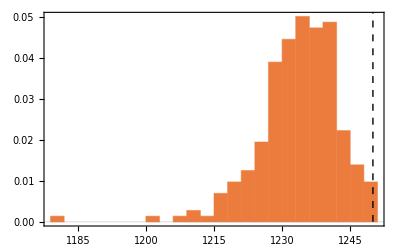

```mathematica
Histogram[W,{3},"PDF",PlotTheme->"Scientific",Epilog->{Dashed,Line[{{1250,0},{1250,100}}]}]
```

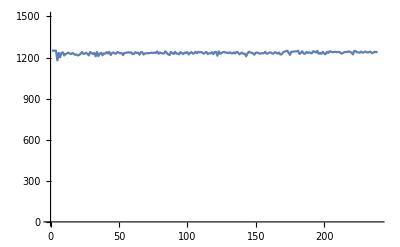

```mathematica
ListLinePlot[(W),PlotRange->{Automatic,{0,1500}}]
```